```mathematica
Import["vicon_input.m"]
Import["datasets.m"]
```

```mathematica
SimpleAnnotator[currentDataset]
```

```mathematica
annotations = LoadAnnotations[];
whichTrack = 3;
tracks = ExtractReach[currentDataset, annotations,whichTrack];
```

```mathematica
planeData = ComputeTrackPlaneData[tracks, wristI];
(*m = PlotTracksArmAndPlane[currentDataset, 600, annotations[[1,2]], 2, tracks[[wristI,2]], tracks[[thumbI,2]], tracks[[pinkieI,2]], tracks[[elbowI,2]], tracks[[shoulderI,2]], planeData[[1,2]]];*)
```

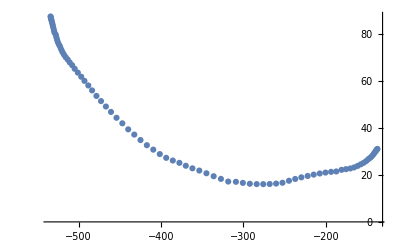

```mathematica
ListPlot[Transpose[planeData[[5,2]]]]
```

```mathematica
wristConic = ComputeConic2D[planeData[[5,2]]]
wristConicParametric = ComputeParametricEllipseFromConic2D[wristConic[[1,2]]]
```

{conicSolution→{0.0000102907,8.14227×10^-7,0.0000607411,0.0055419,-0.0161803,0.999854},conicMat→{{0.0000102907,4.07113×10^-7,0.00277095},{4.07113×10^-7,0.0000607411,-0.00809015},{0.00277095,-0.00809015,0.999854}}}

{conicCenter→{-274.61,135.031},axLens→{118.535,288.037},axVecs→{{0.00806878,0.999967},{-0.999967,0.00806878}},axAlpha→0.00806887}

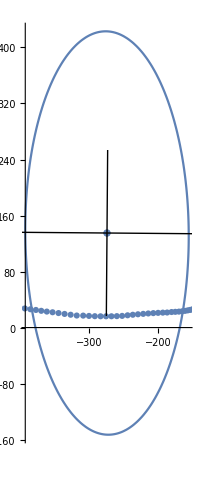

```mathematica
Show[{
ParametricPlot[HomToCart2D[
RigidTrans2D[wristConicParametric[[4,2]],wristConicParametric[[1,2,1]], wristConicParametric[[1,2,2]]].
CartToHom2D[Transpose[{{wristConicParametric[[2,2,1]] * Cos[ppTheta], wristConicParametric[[2,2,2]] * Sin[ppTheta]}}]]
], {ppTheta, -Pi, Pi}],
ListPlot[Transpose[planeData[[5,2]]]],
ListPlot[{wristConicParametric[[1,2]]}],
Graphics[
Line[{wristConicParametric[[1,2]] - wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]], wristConicParametric[[1,2]] + wristConicParametric[[3,2,1]] * wristConicParametric[[2,2,1]]}
]],
Graphics[
Line[
{wristConicParametric[[1,2]] - wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]
, wristConicParametric[[1,2]] + wristConicParametric[[3,2,2]] * wristConicParametric[[2,2,2]]}
]]
(*,
ListPlot[Transpose[HomToCart2D[RigidTrans2D[,VTSWristCenter[[1]], VTSWristCenter[[2]]].CartToHom2D[{ParametricEllipsePt[WristAxLens[[1]], WristAxLens[[2]], uTheta]}]]]]*)
}]
```

```mathematica
PlotRangeParameter = 600;
Manipulate[Show[{
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[8]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[6]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[4]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[1]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],
ListPointPlot3D[
{ViconFrameMat[currentDataset, u][[5]]}
, PlotRange->{{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter},{-PlotRangeParameter, PlotRangeParameter}}],

Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[5]],ViconFrameMat[currentDataset, u][[1]],ViconFrameMat[currentDataset, u][[7]],ViconFrameMat[currentDataset, u][[5]]}]
],
Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[1]],ViconFrameMat[currentDataset, u][[8]],ViconFrameMat[currentDataset, u][[2]],ViconFrameMat[currentDataset, u][[3]],ViconFrameMat[currentDataset, u][[1]]}]
],
Graphics3D[
Line[{ViconFrameMat[currentDataset, u][[8]],ViconFrameMat[currentDataset, u][[6]],ViconFrameMat[currentDataset, u][[4]],ViconFrameMat[currentDataset, u][[8]]}]
]
(*,
ParametricPlot3D[
ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]], ppTheta, Transpose[planeData[[2,2]]]]
,{ppTheta, -Pi, Pi}]*)
}]
, {u, annotations[[1,2,whichTrack,1]],annotations[[1,2,whichTrack,2]], 1}
]
```

```mathematica
Manipulate[Show[{
ListPointPlot3D[ViconTrackSection[currentDataset, 8, annotations[[1,2,whichTrack,1]], annotations[[1,2,whichTrack,2]]]],
ParametricPlot3D[
ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]], ppTheta, Transpose[planeData[[2,2]]]]
,{ppTheta, -Pi, Pi}],
ListPointPlot3D[Transpose[ParametricEllipse3DPt[wristConicParametric, planeData[[4,2]],u, Transpose[planeData[[2,2]]]]],PlotStyle->{Green,PointSize[0.05]}],
ListPointPlot3D[ {ViconTrackSection[currentDataset, 8, annotations[[1,2,whichTrack,1]], annotations[[1,2,whichTrack,2]]][[1]]},PlotStyle->{Red,PointSize[0.05]}]
}]
, {u, -Pi,Pi}
]
```

```mathematica
cnt = ComputeNearestThetas[wristConicParametric, tracks[[1,2]], Transpose[planeData[[2,2]]], planeData[[4,2]]];
cnt
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

{{distance→334.759,theta→-0.358657,onEllipse→{-162.275,-19.8307,-31.8225},interestPt→{-134.319,-283.696,172.278}},{distance→334.819,theta→-0.359848,onEllipse→{-162.327,-19.638,-31.5663},interestPt→{-134.968,-283.642,172.535}},{distance→334.813,theta→-0.361385,onEllipse→{-162.394,-19.3892,-31.2354},interestPt→{-135.783,-283.5,172.816}},{distance→334.746,theta→-0.36373,onEllipse→{-162.498,-19.0102,-30.7314},interestPt→{-136.714,-283.186,173.232}},{distance→334.748,theta→-0.366259,onEllipse→{-162.61,-18.6017,-30.1883},interestPt→{-137.943,-282.943,173.703}},{distance→334.675,theta→-0.369446,onEllipse→{-162.752,-18.0876,-29.5045},interestPt→{-139.301,-282.544,174.261}},{distance→334.727,theta→-0.372989,onEllipse→{-162.911,-17.5167,-28.7454},interestPt→{-141.1,-282.251,174.927}},{distance→334.828,theta→-0.376505,onEllipse→{-163.071,-16.9509,-27.9929},interestPt→{-143.092,-282.028,175.587}},{distance→334.891,theta→-0.379879,onEllipse→{-163.225,-16.4088,-27.2719},interestPt→{-145.453,-281.85,176.142}},{distance→334.768,theta→-0.384242,onEllipse→{-163.427,-15.7089,-26.3412},interestPt→{-148.04,-281.379,176.765}},{distance→334.768,theta→-0.388614,onEllipse→{-163.631,-15.0088,-25.41},interestPt→{-151.139,-281.069,177.385}},{distance→334.695,theta→-0.392949,onEllipse→{-163.835,-14.3159,-24.4884},interestPt→{-154.614,-280.743,177.879}},{distance→334.594,theta→-0.397702,onEllipse→{-164.062,-13.5577,-23.4799},interestPt→{-158.462,-280.354,178.366}},{distance→334.525,theta→-0.402719,onEllipse→{-164.303,-12.759,-22.4176},interestPt→{-162.782,-279.98,178.823}},{distance→334.392,theta→-0.407137,onEllipse→{-164.518,-12.0571,-21.4839},interestPt→{-167.365,-279.652,179.023}},{distance→334.543,theta→-0.411577,onEllipse→{-164.736,-11.353,-20.5473},interestPt→{-172.587,-279.573,179.242}},{distance→334.551,theta→-0.41614,onEllipse→{-164.963,-10.631,-19.5868},interestPt→{-178.026,-279.33,179.297}},{distance→334.683,theta→-0.423091,onEllipse→{-165.312,-9.53392,-18.1273},interestPt→{-184.448,-278.832,179.673}},{distance→334.894,theta→-0.428076,onEllipse→{-165.566,-8.74923,-17.0833},interestPt→{-190.747,-278.626,179.606}},{distance→335.192,theta→-0.434167,onEllipse→{-165.879,-7.79292,-15.811},interestPt→{-197.601,-278.275,179.603}},{distance→335.615,theta→-0.440763,onEllipse→{-166.224,-6.76049,-14.4373},interestPt→{-204.527,-277.873,179.646}},{distance→336.302,theta→-0.448258,onEllipse→{-166.62,-5.59127,-12.8815},interestPt→{-211.858,-277.48,179.807}},{distance→337.113,theta→-0.456413,onEllipse→{-167.058,-4.32401,-11.1952},interestPt→{-219.205,-277.011,180.031}},{distance→338.111,theta→-0.465124,onEllipse→{-167.534,-2.97597,-9.40122},interestPt→{-226.828,-276.533,180.256}},{distance→339.251,theta→-0.474548,onEllipse→{-168.058,-1.52442,-7.46936},interestPt→{-234.352,-275.996,180.577}},{distance→340.684,theta→-0.484657,onEllipse→{-168.63,0.0248502,-5.40728},interestPt→{-241.918,-275.535,181.036}},{distance→342.499,theta→-0.495919,onEllipse→{-169.28,1.74076,-3.12318},interestPt→{-249.813,-275.156,181.669}},{distance→344.42,theta→-0.505129,onEllipse→{-169.821,3.13618,-1.26554},interestPt→{-257.515,-275.059,181.88}},{distance→346.494,theta→-0.514064,onEllipse→{-170.355,4.4831,0.527674},interestPt→{-265.309,-275.037,181.94}},{distance→347.442,theta→-2.62403,onEllipse→{-376.575,2.81059,0.960861},interestPt→{-273.164,-275.156,181.949}},{distance→345.13,theta→-2.63317,onEllipse→{-377.09,1.42276,-0.87313},interestPt→{-281.15,-275.226,181.818}},{distance→343.07,theta→-2.64277,onEllipse→{-377.621,-0.0409628,-2.80758},interestPt→{-289.439,-275.505,181.693}},{distance→341.584,theta→-2.65317,onEllipse→{-378.185,-1.63471,-4.91403},interestPt→{-297.885,-276.278,181.64}},{distance→339.599,theta→-2.66343,onEllipse→{-378.731,-3.21584,-7.004},interestPt→{-306.31,-276.53,181.098}},{distance→337.404,theta→-2.67266,onEllipse→{-379.212,-4.64595,-8.89451},interestPt→{-315.652,-276.417,180.689}},{distance→336.192,theta→-2.68523,onEllipse→{-379.852,-6.60256,-11.4812},interestPt→{-324.468,-277.423,179.867}},{distance→335.099,theta→-2.69737,onEllipse→{-380.456,-8.50539,-13.9971},interestPt→{-333.271,-278.372,178.971}},{distance→334.226,theta→-2.70944,onEllipse→{-381.039,-10.4056,-16.5098},interestPt→{-342.03,-279.391,177.996}},{distance→333.665,theta→-2.72052,onEllipse→{-381.56,-12.1603,-18.8303},interestPt→{-350.654,-280.417,177.169}},{distance→333.423,theta→-2.73031,onEllipse→{-382.01,-13.718,-20.8903},interestPt→{-358.974,-281.409,176.547}},{distance→333.35,theta→-2.74005,onEllipse→{-382.448,-15.2748,-22.9495},interestPt→{-367.005,-282.445,175.806}},{distance→333.666,theta→-2.74984,onEllipse→{-382.877,-16.8454,-25.0269},interestPt→{-374.731,-283.729,175.073}},{distance→333.857,theta→-2.75861,onEllipse→{-383.252,-18.2572,-26.8946},interestPt→{-382.721,-284.634,174.361}},{distance→334.452,theta→-2.7677,onEllipse→{-383.632,-19.727,-28.839},interestPt→{-390.702,-285.818,173.655}},{distance→335.186,theta→-2.77798,onEllipse→{-384.05,-21.3941,-31.0446},interestPt→{-398.474,-287.246,172.583}},{distance→336.045,theta→-2.78908,onEllipse→{-384.489,-23.2008,-33.4352},interestPt→{-406.346,-288.821,171.246}},{distance→337.057,theta→-2.79983,onEllipse→{-384.901,-24.9587,-35.7613},interestPt→{-414.086,-290.397,169.904}},{distance→338.025,theta→-2.81125,onEllipse→{-385.324,-26.8335,-38.2422},interestPt→{-421.791,-291.986,168.216}},{distance→339.182,theta→-2.82278,onEllipse→{-385.736,-28.7317,-40.7545},interestPt→{-429.273,-293.712,166.452}},{distance→340.274,theta→-2.83366,onEllipse→{-386.112,-30.5311,-43.1362},interestPt→{-436.621,-295.224,164.645}},{distance→341.525,theta→-2.84523,onEllipse→{-386.496,-32.4514,-45.678},interestPt→{-443.701,-296.983,162.625}},{distance→342.715,theta→-2.85592,onEllipse→{-386.837,-34.2295,-48.0317},interestPt→{-450.741,-298.471,160.645}},{distance→344.086,theta→-2.86661,onEllipse→{-387.166,-36.0156,-50.3963},interestPt→{-457.399,-300.137,158.654}},{distance→345.284,theta→-2.87631,onEllipse→{-387.453,-37.6402,-52.5473},interestPt→{-463.527,-301.544,156.71}},{distance→346.49,theta→-2.88578,onEllipse→{-387.722,-39.2294,-54.6516},interestPt→{-469.43,-302.922,154.742}},{distance→347.719,theta→-2.89463,onEllipse→{-387.965,-40.7186,-56.6235},interestPt→{-474.956,-304.253,152.878}},{distance→348.755,theta→-2.90371,onEllipse→{-388.204,-42.25,-58.6514},interestPt→{-480.219,-305.506,150.776}},{distance→349.714,theta→-2.91168,onEllipse→{-388.406,-43.5964,-60.4346},interestPt→{-484.745,-306.645,148.907}},{distance→350.534,theta→-2.91914,onEllipse→{-388.589,-44.8581,-62.1055},interestPt→{-489.399,-307.502,147.01}},{distance→351.221,theta→-2.92568,onEllipse→{-388.744,-45.9676,-63.575},interestPt→{-493.284,-308.264,145.299}},{distance→351.966,theta→-2.93216,onEllipse→{-388.892,-47.0679,-65.0324},interestPt→{-497.376,-308.977,143.57}},{distance→352.572,theta→-2.93814,onEllipse→{-389.025,-48.0833,-66.3773},interestPt→{-501.162,-309.541,141.882}},{distance→353.484,theta→-2.94357,onEllipse→{-389.142,-49.0083,-67.6026},interestPt→{-504.204,-310.471,140.601}},{distance→354.197,theta→-2.94799,onEllipse→{-389.235,-49.7611,-68.5998},interestPt→{-507.207,-311.022,139.44}},{distance→354.836,theta→-2.95229,onEllipse→{-389.323,-50.4937,-69.5703},interestPt→{-509.668,-311.653,138.328}},{distance→355.576,theta→-2.95592,onEllipse→{-389.395,-51.1121,-70.3895},interestPt→{-512.109,-312.226,137.444}},{distance→356.057,theta→-2.95972,onEllipse→{-389.469,-51.7612,-71.2495},interestPt→{-514.234,-312.717,136.386}},{distance→356.61,theta→-2.96334,onEllipse→{-389.538,-52.3795,-72.0686},interestPt→{-515.959,-313.362,135.48}},{distance→357.09,theta→-2.96693,onEllipse→{-389.606,-52.9935,-72.8821},interestPt→{-517.449,-314.018,134.568}},{distance→357.683,theta→-2.97073,onEllipse→{-389.675,-53.6427,-73.7422},interestPt→{-518.76,-314.874,133.7}},{distance→358.209,theta→-2.97371,onEllipse→{-389.728,-54.1538,-74.4193},interestPt→{-520.191,-315.458,132.977}},{distance→358.742,theta→-2.97686,onEllipse→{-389.783,-54.6921,-75.1325},interestPt→{-521.416,-316.152,132.249}},{distance→359.336,theta→-2.98012,onEllipse→{-389.839,-55.2508,-75.8728},interestPt→{-522.384,-317.014,131.574}},{distance→359.819,theta→-2.98329,onEllipse→{-389.892,-55.7943,-76.5929},interestPt→{-523.196,-317.816,130.878}},{distance→360.394,theta→-2.98654,onEllipse→{-389.945,-56.3513,-77.331},interestPt→{-523.843,-318.773,130.251}},{distance→360.628,theta→-2.98969,onEllipse→{-389.996,-56.8916,-78.0469},interestPt→{-525.455,-319.071,129.234}},{distance→360.993,theta→-2.99231,onEllipse→{-390.037,-57.3422,-78.644},interestPt→{-526.035,-319.738,128.646}},{distance→361.331,theta→-2.99555,onEllipse→{-390.087,-57.8978,-79.3803},interestPt→{-526.74,-320.467,127.848}},{distance→361.42,theta→-2.99826,onEllipse→{-390.127,-58.3631,-79.9967},interestPt→{-527.328,-320.91,127.052}},{distance→361.549,theta→-3.00092,onEllipse→{-390.166,-58.8196,-80.6017},interestPt→{-527.905,-321.381,126.297}},{distance→361.634,theta→-3.00313,onEllipse→{-390.198,-59.1998,-81.1055},interestPt→{-528.439,-321.734,125.641}},{distance→361.783,theta→-3.00543,onEllipse→{-390.23,-59.5961,-81.6307},interestPt→{-528.993,-322.155,124.996}},{distance→361.76,theta→-3.0071,onEllipse→{-390.253,-59.8831,-82.0111},interestPt→{-529.467,-322.32,124.427}},{distance→361.608,theta→-3.0093,onEllipse→{-390.283,-60.2611,-82.5119},interestPt→{-529.779,-322.545,123.664}},{distance→361.62,theta→-3.01048,onEllipse→{-390.299,-60.4647,-82.7818},interestPt→{-530.145,-322.675,123.271}}}

```mathematica
ListPlot[DisceteD[thetas]]
ListPlot[ComputeNorms[DisceteD[ellipsePositions]]]
ListPlot[ComputeNorms[DisceteD[originalPositions]]]
ListPlot[ComputeNorms[DisceteD[DisceteD[ellipsePositions]]]]
ListPlot[ComputeNorms[DisceteD[DisceteD[originalPositions]]]]
```

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

Part::partw: Part 1 of {} does not exist.

-Graphics-

```mathematica
LinesAlong[ellipsePositions]
LinesAlong[DisceteD[ellipsePositions]]
LinesAlong[DisceteD[originalPositions]]
```

Part::partw: Part 1 of {} does not exist.

-Graphics3D-

Part::partw: Part 1 of {} does not exist.

-Graphics3D-

Part::partw: Part 1 of {} does not exist.

-Graphics3D-